# Chiense word cloud

```mathematica
SystemInformation["Small"]
```

{Kernel→{SystemID→MacOSX-x86-64,ReleaseID→10.3.0.0 (5416302, 2015100902),CreationDate→Fri 9 Oct 2015 18:38:23GMT-8.},FrontEnd→{OperatingSystem→MacOSX,ReleaseID→10.3.0.0 (5416302, 2015100903),CreationDate→Fri 9 Oct 2015 19:32:00GMT-8.}}

```mathematica
myChineseStr="词云在外语学习中有着开拓式的应用。在优秀的最新电子学习网站中。经有使用
人工智能方式辅助用户进行外语单词的学习。采用自动分析的方法， 进行概率统计与与分析后，提供给外语学习者相应的词汇表与词云图。
  教育工作者，可以利用Wordle工具，以加强学习。 提供阅读整个信息的新重点，提供给学生，揭示关键概念并使用新的模式看到以前
看不到的新颖材料，预计这种工具会得到广泛的应用。词云有可能成 为最新的计算机辅助外语学习的新形式。文化在小说阅读中，词云图会提示关键词和主题索
引。方便用户在互联网上快速阅读。在娱乐中，变幻莫测的词云图给 用户提供充分的想象空间和娱乐趣味。可以相互采用彩云图卡片进行教育与娱乐。也可以将
这些词云图保存打印下来，或者印在 T-Shirt 、明信片上，甚至是放到自己的网络相簿内，都是展现自己极佳的方式。
  计算机软件国外已经研究并开发了相应的软件-Wordle。Wordle是一个用于从文本生成词云图而提供的游戏工具。图会更加突出话
题并频繁地出现在源文本。可以调整不同的字体，布局 和配色方案。用图像与Wordle创建喜欢的模式。可以打印出来或储存与朋友一起欣赏。";
```

```mathematica
Clear[segmentedChineseWords]
segmentedChineseWords[ChineseStr_String]:=Import[If[$VersionNumber≥10,"!curl -A Mozilla/4.0 ",""]<>"http://alphalocalizationvm.wolfram.com:11200/?key="<>URLEncode[ChineseStr],"JSON"];
```

```mathematica
segmentedChineseWords["苹果橘子大头"]
```

{苹果,橘子,大头}

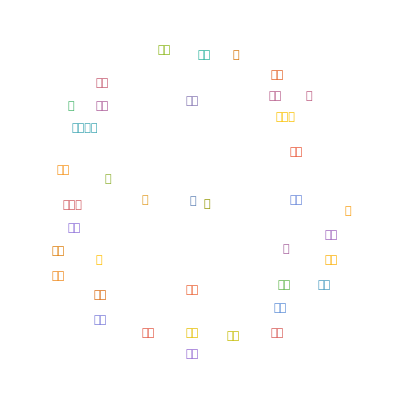

```mathematica
WordCloud[segmentedChineseWords[StringTake[myChineseStr,100]]]
```

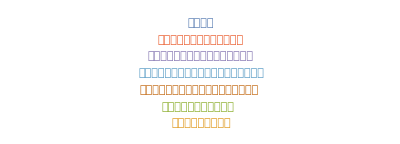

```mathematica
WordCloud[StringTake[myChineseStr,100]]
```